# Problem 1.1, Time delayed model with Allee effect

## for February 09, 23.59, 2024

## It is well-known that individuals in many biological populations suffer from a reduced capacity to reproduce or survive when the population density (that is, size) is small. As a consequence, the population may experience extinction depending on its density. This effect is known as Allee effect [W. C. Allee et al. Principles of animal ecology (1949)]. The Allee effect can arise due to several different mechanisms, such as difficulty of finding a mate, inefficient antipredator strategies in small groups of prey (due to reduced cooperation) etc. Mechanisms that allow for the Allee effect to appear (for example reduced cooperation) are often time delayed. Denoting the population size by N, a time-delayed growth with Allee effect can be modelled as follows: Here is a time-delay parameter. Your task is to analyse how the dynamics in this model depends on the time-delay parameter . Solve Eq. (1) numerically. Integrate Eq. (1) for , up to 5. Set the remaining parameters to: , , , and (where denotes the population size at time t = 0). Assume further that during the time interval the population size was constant and equal to .

## a) Show examples of the different dynamics obtained in this model: no oscillations, damped oscillations, and stable oscillations (limit cycle).

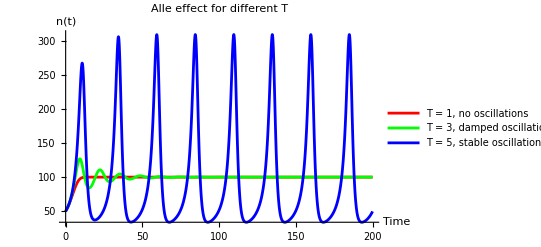

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = 50;
TValues = {1, 3, 5};
t0 = 0;
tMax = 200;

solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), n[t /; t<=0]==initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

legends = {
	"T = 1, no oscillations", 
	"T = 3, damped oscillations", 
	"T = 5, stable oscillations (limit cycles)"
};

colors = {
	Red,
	Green,
	Blue
};

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> legends, 
     PlotLabel -> "Alle effect for different T", 
     AxesLabel -> {"Time", "n(t)"},
     PlotStyle->colors,
     ImageSize->Full
]
```

One can see in the plot above different dynamics: without any oscillation (red), damped oscillation (green), and stable oscillations (blue). This was calculated using a continuous approach with time delay. To apply this  Mathematica provides a numerical solver called by NDSolveValue. The time delay was implemented using n[t /; t<=0]==initialCondition set the population to the initialCondition until a time delay T was passed.

## b) Estimate numerically with one decimal precision the value of T at which the dynamics starts exhibiting damped oscillations.

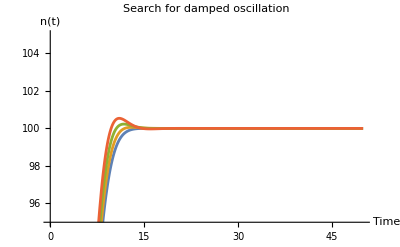

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

The maximum value of the solution with T = 1 is {100.003,{t→15.7951}}

The maximum value of the solution with T = 1.1 is {100.058,{t→12.9973}}

The maximum value of the solution with T = 1.2 is {100.229,{t→11.7693}}

The maximum value of the solution with T = 1.3 is {100.537,{t→11.0303}}

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = 50;
TValues = {1, 1.1, 1.2, 1.3};
t0 = 0;
tMax = 50;

solveDifferentialEquation[T_] := NDSolveValue[
    {n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), n[t /; t<=0]==initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
    solveDifferentialEquation[T], 
    {T, TValues}
];

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> {{t0, tMax}, {95, 105}}, 
     PlotLabel -> "Search for damped oscillation", 
     AxesLabel -> {"Time", "n(t)"},
     ImageSize->Full
]

(* New code to print the maximum value of each solution *)
maxValues = Table[
    FindMaximum[{solutions[[i]][t]},{t,7}], 
    {i, Length[TValues]}
];

(* Print the maximum values *)
Do[
    Print["The maximum value of the solution with T = ", TValues[[i]], " is ", maxValues[[i]]], 
    {i, Length[TValues]}
];
```

The object of finding the first damped oscillation is fairly easy. This has to do with the fact that a dampening can only occur if the dynamics studied are higher than the dynamics for no oscillation. Thus from the plot it seem evident that the damped oscillation starts as soon as , but nevertheless the numerical search also indicates that for  the values go above  for the first time, ignoring the small numerical approximation error of .

## c) Estimate numerically with one decimal precision the value of T (denoted by ) at which a bifurcation (Hopf bifurcation) occurs.

{0.900938,0.940115,0.957796,0.967826,0.974273,0.978765,0.982076,0.984621,0.986642,0.988287,0.989654,0.990808,0.991796,0.992651,0.993397,0.994054,0.994634,0.995151,0.995612,0.996025,0.996396,0.99673,0.997032,0.997305,0.997551,0.997774,0.997977,0.998161,0.998327,0.998479,0.998616,0.998741,0.998855,0.998958,0.999052,0.999138,0.999215,0.999286,0.99935,0.999409,0.999462,0.99951,0.999555,0.999595,0.999631,0.999664,0.999695,0.999722,0.999747,0.99977,0.999791,0.999809,0.999827,0.999842,0.999856,0.999869,0.999881,0.999892,0.999906,0.99991,0.999918,0.999926,0.999932,0.999938}

{0.911801,0.947648,0.963732,0.972728,0.978409,0.982287,0.985083,0.987184,0.988812,0.990107,0.991159,0.992027,0.992755,0.993373,0.993903,0.994362,0.994764,0.995118,0.995431,0.995711,0.995962,0.996188,0.996393,0.996579,0.996749,0.996905,0.997049,0.997181,0.997304,0.997418,0.997523,0.997622,0.997714,0.997801,0.997882,0.997958,0.99803,0.998098,0.998162,0.998222,0.99828,0.998335,0.998387,0.998436,0.998483,0.998528,0.998571,0.998612,0.998651,0.998689,0.998725,0.99876,0.998793,0.998825,0.998856,0.998886,0.998914,0.998942,0.998968,0.998994,0.999019,0.999043,0.999066}

{0.924371,0.956679,0.971222,0.979307,0.984363,0.987774,0.990202,0.991998,0.993368,0.99444,0.995293,0.995985,0.996552,0.997023,0.997417,0.99775,0.998034,0.998277,0.998485,0.998666,0.998823,0.998959,0.999078,0.999183,0.999275,0.999356,0.999427,0.99949,0.999546,0.999595,0.999639,0.999678,0.999712,0.999743,0.99977,0.999795,0.999817,0.999836,0.999853,0.999869,0.999883,0.999895,0.999906,0.999916,0.999925,0.999933,0.99994,0.999946,0.999952,0.999957,0.999961,0.999965,0.999969,0.999972,0.999975,0.999978,0.99998,0.999982,0.999984,0.999986,0.999987}

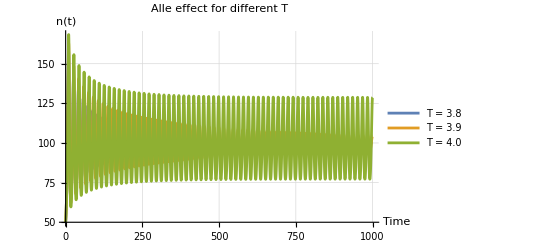

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = 50;
TValues = {3.8,3.9,4.0}; (*3.9,4.4,4.5*)
t0 = 0;
tMax = 1000;

solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), n[t /; t<=0]==initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

data = Table[solutions[[i]][t], {t, t0, tMax, 0.0001}, {i, Length[TValues]}];
data1 = data[[All,1]];
data2 = data[[All,2]];
data3 = data[[All,3]];
peaks1 = FindPeaks[data1];
peaks2 = FindPeaks[data2];
peaks3 = FindPeaks[data3];

ratios1 = Table[peaks1[[i+1, 2]] / peaks1[[i, 2]], {i, 1, Length[peaks1] - 1}]
ratios2 = Table[peaks2[[i+1, 2]] / peaks2[[i, 2]], {i, 1, Length[peaks2] - 1}]
ratios3 = Table[peaks3[[i+1, 2]] / peaks3[[i, 2]], {i, 1, Length[peaks3] - 1}]


legends = {
	"T = 3.8", 
	"T = 3.9", 
	"T = 4.0"
};

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends->legends,
     PlotLabel -> "Alle effect for different T", 
     GridLines->Automatic,
     AxesLabel -> {"Time", "n(t)"},
     ImageSize->Full
]
```

The plot shows dynamics for the  values of 3.8 (blue), 3.9 (yellow) and 4.0 (green). Analysing it graphically it is evident that for  the dynamics go over to a stable oscillations (limit cycle) thus the I set the =4. If one is not convinced by this graphical estimation the behaviour can also be shown analytically. Have look at Out[301], it shows the ratio between the next node divided by the current node. One can see converging behaviour to 1 in the long run.

## d) Use linear stability analysis to analytically compute the value of . Do this by linearising Eq. (1) around the steady state and use a perturbation that is proportional to . Compare that you obtain analytically to the estimate found in subtask c). Discuss your results.

The following stability analysis found , which is not exactly what is found in c) where  .  It is quiet obvious from the plot that for  the motion is a damped oscillation thus the approximated answer in c) is still correct, because the Hopfbifurcation can not happen if  is not larger than .